```mathematica
rovI1=(iL[t]==iR1[t]+iR2[t]);
rovI2=(iR2[t]==iC2[t]);
rovI3=(iR1[t]==iC1[t]);
rovR1=(u2[t]-u4[t]==iR1[t]*R1);
rovR2=(u2[t]-u3[t]==iR2[t]*R2);
rovC1=(iC1[t]==C1*u4'[t]);
rovC2=(iC2[t]==C2*u3'[t]);
rovL=(uz[t]-u2[t]==L *iL'[t]);
poc1=(u4[0]==0);
poc2=(u3[0]==0);
poc3=(iL[0]==0);
rceU4 = rovC1/.Solve[rovI3,iC1[t]]/.Solve[rovR1,iR1[t]]
rceU3 = rovC2/.Solve[rovI2,iC2[t]]/.Solve[rovR2,iR2[t]]
rceI=rovI1/.Solve[rovI2,iR2[t]]/.Solve[rovI3,iR1[t]]
```

{{(u2[t]-u4[t])/R1==C1 u4'[t]}}

{{(u2[t]-u3[t])/R2==C2 u3'[t]}}

{{iL[t]==iC1[t]+iC2[t]}}

```mathematica
rov={rceI,rceU3,rceU4,rovL,rovC1,rovC2,poc1,poc2,poc3}//Flatten;
promene={iC1[t],iC2[t],u2[t],u4[t],u3[t],iL[t]};

dosad={R1-> 20000,R2-> 10000,L-> 10*10^(-3),C1-> 22*10^(-9),C2-> 33*10^(-9)};
f=10.;
ampl=3.3;
perioda=1/f;
tmax=perioda/10;
(*uz=10*)
uz[t_]:=ampl*Tanh[100*Sin[2*Pi*f*t/perioda]]

res=NDSolve[Evaluate[rov/.dosad],promene,{t,0,tmax},MaxSteps->10^8]
```

{{iC1[t]→InterpolatingFunction[{{0.,0.01}},<>][t],iC2[t]→InterpolatingFunction[{{0.,0.01}},<>][t],u2[t]→InterpolatingFunction[{{0.,0.01}},<>][t],u4[t]→InterpolatingFunction[{{0.,0.01}},<>][t],u3[t]→InterpolatingFunction[{{0.,0.01}},<>][t],iL[t]→InterpolatingFunction[{{0.,0.01}},<>][t]}}

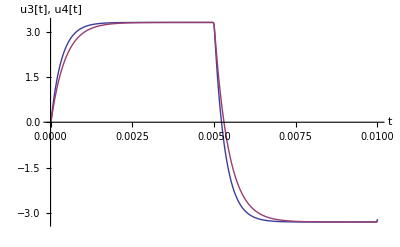

```mathematica
Plot[{u3[t],u4[t]}/.res//Evaluate,{t,0,tmax},AxesLabel->{"t","u3[t], u4[t]"},PlotStyle->{Thick}]
```

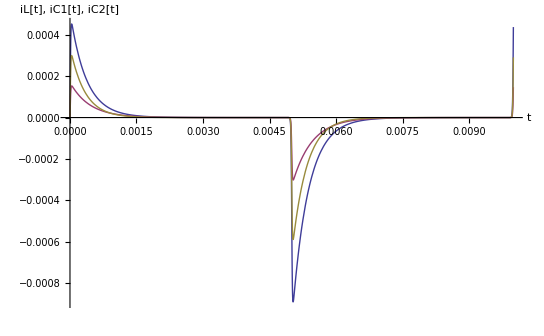

```mathematica
Plot[{iL[t],iC1[t],iC2[t]}/.res//Evaluate,{t,0,tmax},PlotRange->All,AxesLabel->{"t","iL[t], iC1[t], iC2[t]"},PlotStyle->{Thick}]
```